## Study the behavior of the oscillator frequencies ω_1 and ω_2

```mathematica
ClearAll["Global`*"]
```

```mathematica
S[I_,j_]:=(2I-1-2j)/(2I-1);
SP[I_,j_]:=(2j-2I-1)/(2j-1);
T[j_,γ_]:=1/(j(j+1))Sqrt[3](Sqrt[3]Cos[γ]+Sin[γ]);
TP[j_,γ_]:=1/(j(j+1))2Sqrt[3]Sin[γ];
```

### Create the omega sub-terms

### Nuclear total spin -> i Single-particle spin -> j

```mathematica
st1[i_,j_,a1_,a3_]:=(2i-1)(a3-a1)+2*j*a1;
st2[i_,j_,a1_,a2_]:=(2i-1)(a2-a1)+2*j*a1;
st3[i_,j_,a1_,a3_,v_,γ_]:=(2j-1)(a3-a1)+2*i*a1+v*(2j-1)/(j(j+1))Sqrt[3](Sqrt[3]Cos[γ]+Sin[γ]);
st4[i_,j_,a1_,a2_,v_,γ_]:=(2j-1)(a2-a1)+2i*a1+v*(2j-1)/(j(j+1))2Sqrt[3]*Sin[γ];
```

```mathematica
omega1[i_,j_,a1_,a2_,a3_]:=(st1[i,j,a1,a3]*st2[i,j,a1,a2])^(1/2);
omega2[i_,j_,a1_,a2_,a3_,v_,γ_]:=(st3[i,j,a1,a3,v,γ])^(1/2)*(st4[i,j,a1,a2,v,γ])^(1/2);
```

### Numerical interpretation

```mathematica
j0=13/2;
A1=0.05;
V=3;
γ=25*π/180;
```

## Create numerical data

### Omega1

```mathematica
Print[{A1,A1*S[spin,j0]}/.{spin->35/2}]
```

{0.05,0.0308824}

### Omega2

```mathematica
Print[{A1,SP[spin,j0]*A1-V*TP[j0,γ],SP[spin,j0]*A1-V*T[j0,γ]}/.{spin->35/2}]
```

{0.05,-0.185925,-0.308198}

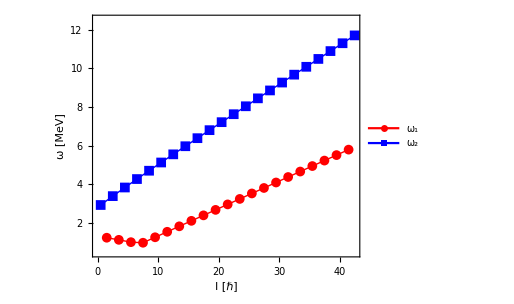

```mathematica
data1=Table[{i,omega1[i,j0,A1,A1+Abs[A1*S[i,j0]],2A1+Abs[A1*S[i,j0]]]},{i,3/2,85/2,2}];
data2=Table[{i,omega2[i,j0,A1,A1+Abs[SP[i,j0]*A1-V*TP[j0,γ]],2A1+Abs[SP[i,j0]*A1-V*T[j0,γ]],V,γ]},{i,1/2,85/2,2}];
fig1=ListPlot[{data1,data2},Joined->True,PlotMarkers->{Automatic, Medium},Frame->True,Axes->False,FrameStyle->Directive[Black, Thick],PlotStyle->{{Red,Thick},{Blue,Thick}},AspectRatio->0.8,FrameLabel->{"I [ℏ]","ω [MeV]"},LabelStyle->{19,Bold,Black,FontFamily->"Arial"},PlotLegends->Placed[{"ω_1","ω_2"},{0.4,0.8}],PlotRange->{Full,{0.5,12.5}},ImageSize->380];
Show[fig1]
Export["/Users/basavyr/Documents/Work/DFT/mathematica-useful-algorithms/Physics/wobbling-frequency-algebraic/omega-1-2-frequencies.pdf",Show[fig1]];
```

```mathematica
data1
data2
```

{{3/2,1.249},{7/2,1.14018},{11/2,1.0198},{15/2,0.989949},{19/2,1.27279},{23/2,1.55563},{27/2,1.83848},{31/2,2.12132},{35/2,2.40416},{39/2,2.68701},{43/2,2.96985},{47/2,3.25269},{51/2,3.53553},{55/2,3.81838},{59/2,4.10122},{63/2,4.38406},{67/2,4.6669},{71/2,4.94975},{75/2,5.23259},{79/2,5.51543},{83/2,5.79828}}

{{1/2,2.93906},{5/2,3.3973},{9/2,3.84255},{13/2,4.27888},{17/2,4.70875},{21/2,5.1338},{25/2,5.55513},{29/2,5.97353},{33/2,6.38958},{37/2,6.80369},{41/2,7.21622},{45/2,7.62741},{49/2,8.03747},{53/2,8.44657},{57/2,8.85484},{61/2,9.26238},{65/2,9.6693},{69/2,10.0757},{73/2,10.4815},{77/2,10.887},{81/2,11.292},{85/2,11.6967}}